## Load Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/khilbert/gitrepos/black-holes-stack/stack/grid

Set the name of the model to load the power spectrum mode function results from.

```mathematica
modelname="testmodel";
```

Load in the rhoC data.

```mathematica
{rvals,rhoCvals}=Import["../../models/"<>modelname<>"/grid.csv"][[2;;]]//Transpose;
```

Plot rhoC vs. radius

```mathematica
ListPlot[Transpose[{rvals, rhoCvals}],Joined->True, InterpolationOrder->3,PlotRange->{{0,5},{0,1}}]
index= Position[rhoCvals,_?(#<0.5&)][[1]] (* First index for which rhoC falls below 0.5 *)
FWHM = rvals[[index-1]][[1]]
```

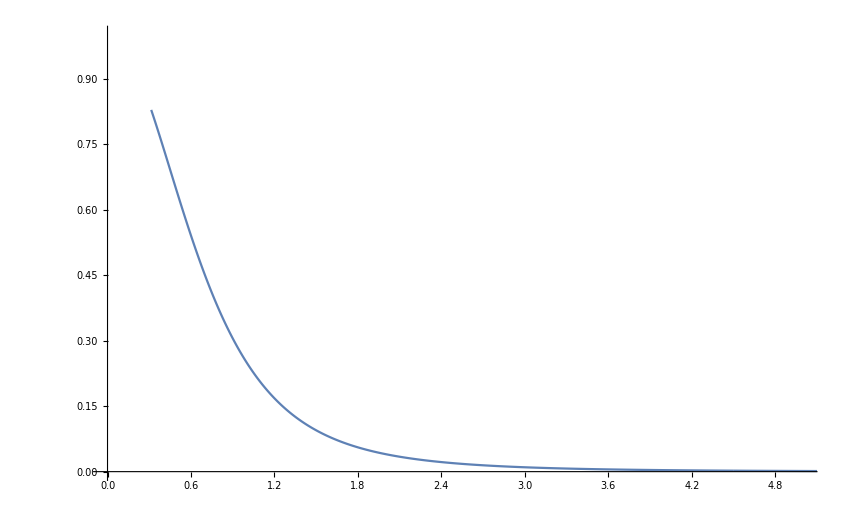

{106}

0.640893

Find the FWHM radius, i.e. when rhoC falls below 0.5

```mathematica
index= Position[rhoCvals,_?(#<0.5&)][[1]] (* First index for which rhoC falls below 0.5 *);
FWHM = rvals[[index-1]][[1]]
```

0.640893